```mathematica
(*Finite Element Method*)
```

```mathematica
(*Parameter initialization*)
SetDirectory[NotebookDirectory[]];
elemFilename="helmelems.dat";
nodeFilename="helmnodes.dat";
height=20;(*The number of elements on the left and right edge of the flow*)
origin = 61;(*Node ID of the location of the Dirichlet boundary singularity*)
inflow=1;(*Flow in and out of the left/right edges*)
scale=.5;(*Flow field arrow display scale*)
Δx=.01;(*Streamline resolution*)
Δy=.01;(*Streamline resolution*)
```

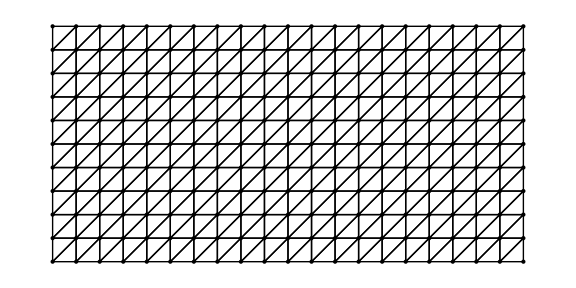

```mathematica
(*Geometry initialization*)

(*elementRecord[[i]] = The node element array for the ith element*)
(*elementRecord[[i]][[j - 1]] = The jth node of element i, counting from bottom left going counterclockwise*)(*Structure: The elements should be in a grid with the first column where the flow enters and the last column where the flow leaves.*)
elementRecord =Import[elemFilename];

(*nodeRecord[[i]] = The coordinates array for the ith node*)
(*nodeRecord[[i]][[j]] = The x or y coordinate of the node; x is j = 2, y is j = 3*)
nodeRecord=Import[nodeFilename];

(*Preliminary node layout*)
getNodes[i_]:=Delete[elementRecord[[i]],1];
getNodes::usage="Returns the nodes {N1, N2, N3} of element i in counterclockwise order from the bottom left.";
getLocation[i_]:=Delete[nodeRecord[[i]],1];
getLocation::usage="Returns the coordinates {x, y} of node i.";

lineArray=ConstantArray[0,{Length[elementRecord]}];
pointArray=ConstantArray[0,{Length[nodeRecord]}];

(*For every element, draw the edges that make up the element*)
For[elt=1,elt≤Length[elementRecord],elt++,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[2]]][[1]];
δ=getLocation[getNodes[elt][[2]]][[2]];
μ=getLocation[getNodes[elt][[3]]][[1]];
ν=getLocation[getNodes[elt][[3]]][[2]];
(*Draw the triangle from (α,β) to (γ,δ) to (μ,ν)*)
lineArray[[elt]]=Line[{{α,β},{γ,δ},{μ,ν},{α,β}}];
]
(*For every node, add its coordinates to be drawn*)
For[node=1,node≤Length[nodeRecord],node++,
pointArray[[node]]=Point[{getLocation[node][[1]],getLocation[node][[2]]}];
]
(*Display the mesh*)
Show[Graphics[lineArray],Graphics[{PointSize[Large],pointArray}],ImageSize-> Large]
```

```mathematica
(*Basis polynomials*)
Ne1:={((γ-x)/(γ-α))*((ν-y)/(ν-β)),((x-α)/(γ-α))*((ν-y)/(ν-β)),((μ-x)/(μ-α))*((y-β)/(ν-β))};
Ne2:={((γ-x)/(γ-α))*((ν-y)/(ν-β)),((x-α)/(γ-α))*((y-β)/(δ-β)),((γ-x)/(γ-μ))*((y-β)/(ν-β))};
(*Basis: first three are the i = 1, 2, 3, second three are for the other facing triangle*)
```

```mathematica
(*Matrix initialization*)
Kij =ConstantArray[0, {Length[nodeRecord],Length[nodeRecord]}];

(*Element loop: establish the square matrix*)
For[elt=1,elt≤Length[elementRecord],elt++,
(*For any given element, initialize the coordinates of the corners*)
(*Calculate the integral for each pair (i, j) of basis polynomials*)
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[2]]][[1]];
δ=getLocation[getNodes[elt][[2]]][[2]];
μ=getLocation[getNodes[elt][[3]]][[1]];
ν=getLocation[getNodes[elt][[3]]][[2]];
(*Depending on what type of triangle we have the integration has different bounds and we have different basis polynomials*)
If[Mod[elt,2]==1,
Kij[[getNodes[elt][[i]],getNodes[elt][[j]]]]+=Integrate[D[Ne1[[i]],{{x,y}}].D[Ne1[[j]],{{x,y}}],{x,α,γ},{y,β,((ν-β)/(μ-α))(x-α)+β}]
];
If[Mod[elt,2]==0,
Kij[[getNodes[elt][[i]],getNodes[elt][[j]]]]+=Integrate[D[Ne2[[i]],{{x,y}}].D[Ne2[[j]],{{x,y}}],{x,α,γ},{y,((δ-β)/(γ-α))(x-α)+β,ν}]
];
];
];
];
```

```mathematica
Mij =ConstantArray[0, {Length[nodeRecord],Length[nodeRecord]}];

(*Element loop: establish the square matrix*)
For[elt=1,elt≤Length[elementRecord],elt++,
(*For any given element, initialize the coordinates of the corners*)

(*Calculate the integral for each pair (i, j) of basis polynomials*)
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[2]]][[1]];
δ=getLocation[getNodes[elt][[2]]][[2]];
μ=getLocation[getNodes[elt][[3]]][[1]];
ν=getLocation[getNodes[elt][[3]]][[2]];

(*Again, depends on the type of triangle we have*)
If[Mod[elt,2]==1,
Mij[[getNodes[elt][[i]],getNodes[elt][[j]]]]+=Integrate[Ne1[[i]]*Ne1[[j]],{x,α,γ},{y,β,((ν-β)/(μ-α))(x-α)+β}]
];
If[Mod[elt,2]==0,
Mij[[getNodes[elt][[i]],getNodes[elt][[j]]]]+=Integrate[Ne2[[i]]*Ne2[[j]],{x,α,γ},{y,((δ-β)/(γ-α))(x-α)+β,ν}]
];
];
];
];
```

```mathematica
(*Set Dirichlet condition to arrive at an analytical solution: place the identity matrix row at the top of both matricies*)
DirichletRow = ConstantArray[0,{Length[nodeRecord]}];
DirichletRow[[1]] = 1;
Kij[[1]]=DirichletRow;
Mij[[1]]=DirichletRow;
```

```mathematica
(*Solve the linear system (K-λM)α=0*)
ev=Eigenvalues[{Kij,Mij}];
αv=Eigenvectors[{Kij,Mij}];
```

```mathematica
(*Postprocessing*)
(*wave heights*)
heightArray = ConstantArray[0,Length[elementRecord]];
waves=ConstantArray[0,Length[ev]];
(*This is the index of the eigenvalue we want to use*)
For[λi=1, λi≤Length[ev],λi++,
(*Given an element, compute the height of the wave at the centroid of that element*)
For[elt=1,elt≤Length[elementRecord],elt++,
α=getLocation[getNodes[elt][[1]]][[1]];
β=getLocation[getNodes[elt][[1]]][[2]];
γ=getLocation[getNodes[elt][[2]]][[1]];
δ=getLocation[getNodes[elt][[2]]][[2]];
μ=getLocation[getNodes[elt][[3]]][[1]];
ν=getLocation[getNodes[elt][[3]]][[2]];
cx=(α+γ)/2;
cy=(β+ν)/2;
(*depending on the triangle we have there will be different basis polynomials for the facing*)
If[Mod[elt,2]==1,
heightArray[[elt]]={cx, cy, Sum[αv[[λi]][[getNodes[elt][[i]]]]*Ne1[[i]]/.{x->cx,y->cy},{i, 1, 3}]};
];
If[Mod[elt,2]==0,
heightArray[[elt]]={cx,cy,Sum[αv[[λi]][[getNodes[elt][[i]]]]*Ne2[[i]]/.{x->cx,y->cy},{i, 1, 3}]};
];
]
waves[[λi]]=ListPlot3D[heightArray, PlotRange-> {-.15,.15}];
]
waves
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}